# Cost of Dai Collateral Attack

```mathematica
LiquidationThreshold = 1.5;
DaiCirculation =77000000;
EthCollateral = 355000000;
KeeperDiscount = 0.03;
AvgTxPrice = 0.20;
CDPOpenNumTx =2;
CDPClosingNumTx = 6;
PETHEx = 1.04;
```

## Decrease overall collateral

```mathematica
collateral[g_] = (EthCollateral - g * DaiCirculation) / (g - LiquidationThreshold);
```

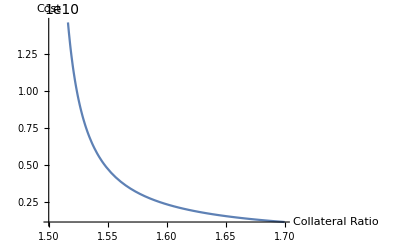

```mathematica
Plot[collateral[i],{i,1.5,1.7}, AxesLabel->{"Collateral Ratio", "Cost"}]
```